# Regulatory and Signaling pathways

## A computational study towards understanding models of molecular networks

Emma Hokken 10572090
Natasja Wezel 11027649

## Complex biomolecular systems can often not be reduced to elementary properties of individual components. Mathematical models that can explain and predict cellular functions are very useful to understand and engineer them. Two of the main methods used today to model molecular and gene networks are: continuous (quantitative) and discrete (qualitative) modelling.

## Analysing mathematical models of signal-response systems Quantitative chemical kinetic models

Biochemical and cellular processes follow chemical and physical laws. If underlying chemical processes are known, the basis of thermodynamical and chemical kinetics can describe the behaviour of a system. Applying system theory to chemical kinetics is the most common approach to model molecular networks. Chemical kinetics uses the notion of processes where reactants are consumed and products are generated.

The rate at which these processes take place is dependent on the quantity of the components involved, reaction order and parameters. The mathematical expressions depend on the assumptions that are made.

-Graphics-
Figure 1. Some simple networks with different dynamic behaviors. S = Signal strength (e.g. concentration of mRNA), R = Response Element (e.g. protein concentration), E = Enzyme, EP = Phosphorylated Enzyme. A) Perfect Adaptation. B-D) Other simple networks, with other types of feedback.

Figure 1a shows a network for perfect adaption. This behaviour is typical of chemotactic systems that respond to an abrupt change in attractants or repellents and then adapt to a constant level of signal.
The kinetic equations for a system with perfect adaption are derived using the law of mass action:

ⅆR/ⅆt=k_1 S-k_2 X R,     with k_1=k_2=2,k_3=k_4=1
ⅆX/ⅆt=k_3 S-k_4 X

For three other types of feedback, different kinetic equations are defined.

Negative feedback: Homeostasis

	ⅆR/ⅆt=k_0 E(R)-k_2 S R
E(R)=G(k_3,k_4 R,J_3,J_4)  	with k_0 = 1, k_2= 1, k_3= 0.5, k_4= 1, J_3= J_4= 0.01. 
	
Positive Feedback: Mutual inhibition

	ⅆR/ⅆt=k_0+k_1 S-k_2 R-k'_2 E(R) R
E(R)=G(k_3,k_4 R,J_3,J_4)		with k_0 = 0, k_1= 1, k_2= 0.05, k'_2= 0.5, k_3= 1, k_4= 0.2, J_3= J_4= 0.05.

Positive Feedback: Mutual activation

	ⅆR/ⅆt=k_0 E_p(R)+k_1 S-k_2 R
E_p(R)=G(k_3 R,k_4,J_3,J_4)	with k_0 = 0.4, k_1= 0.01, k_2= k_3= 1, k_4= 0.2, J_3= J_4= 0.05.

G refers to the Goldbeter-Koshland function and is defined as: 
	G(u,v,J,K)=(2u K)/(v-u+v J+u K+√((v - u + v J + u K)^2- 4(v-u)u K))

Methods
We look at the different dynamic behaviors that the different simple networks in Figure 1 express. To look at the dynamics of the systems, we need to solve them assuming a steady-state.  For each of the networks (1a-d) we will first plot the reaction rate as a function of R and a constant S. For network 1a (perfect adaption) the concentrations of all the species over time (t = 0 - 20) are plotted. S is defined in incremental steps with values S = 0, 1, 2, 3 and 4, each step lasting t = 4. It is investigated whether a signal response curve can actually be plotted. For networks 1b-d, the rates are plotted with different values of S: for homeostasis we take S = 0.5, 1.0, and 1.5, for mutual inhibition we take S = 1.0, 1.5, and 2.0 and for mutual activation we take S = 0.0, 8.0, and 16.0. Then, for networks 1b-d, we will look at signal-response curves. 

Results and Discussion

First, the ODEs are rewritten. They are both set equal to zero, as we solve the system while it is in a steady state. For dX/dt, this leaves us with an expression for X.

ⅆX/ⅆt=k_3 S-k_4 X = 0 
k_3 S=k_4 X
X=k_3 S=k_3 S-k_4 X
X =(k_3 S)/k_4

Plugging this X into the other equation, and also setting it to zero, this leaves us with two rate equations, which can be plotted.
ⅆR/ⅆt=k_1 S-k_2 X R =k_1 S-(k_2 k_3 S)/k_4 R  = 0

v1 = k_1 S
v2 = (k_2 k_3 S)/k_4 R

This process is repeated with the ODEs for the other systems.

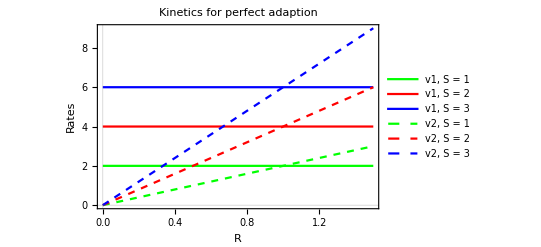

```mathematica
paramsA={k1->2,k2->2,k3->1,k4->1};
rateqsA={v1->k1*s,v2->k2*k3*s*r/k4};

(*Plot rates as a function of R at constant S*)
Plot[{v1/.rateqsA/.paramsA/.s->1,v1/.rateqsA/.paramsA/.s->2,v1/.rateqsA/.paramsA/.s->3,v2/.rateqsA/.paramsA/.s->1,v2/.rateqsA/.paramsA/.s->2,v2/.rateqsA/.paramsA/.s->3},{r,0,1.5},
Frame->True,
FrameLabel->{"R","Rates"},PlotLegends->{"v1, S = 1","v1, S = 2","v1, S = 3","v2, S = 1", "v2, S = 2" , "v2, S = 3"},PlotLabel->Style["Kinetics for perfect adaption",FontSize->18],
PlotTheme->"Scientific",
PlotStyle-> {Green, Red, Blue, {Dashed, Green}, {Dashed, Red}, {Dashed, Blue}}]
```

We see here that both v1 and v2 increase as S increases, which is expected as both are dependent on S. However, when inspecting this graph by eye, we see that for each value of S, the equilibrium (intersection of v1 and v2) is still roughly at the same location. This is expected, as the equilibrium point stays the same (the equilibrium point is independent of S).

Next, the concentrations of all the species over time is plotted. S is defined in incremental steps with values S = 0, 1, 2, 3 and 4, each step lasting t = 4.

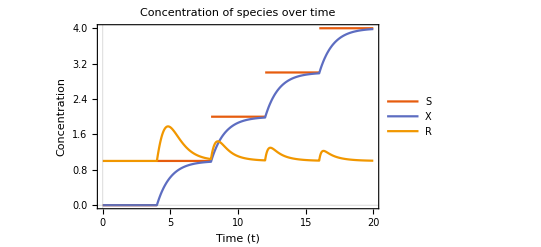

```mathematica
solT[t_] = NDSolve[{r'[t] == 2*Floor[t/4] - 2 * x[t] * r[t], x'[t] == 1* Floor[t/4] - 1*x[t], r[0] == 1, x[0]== 0}, {r[t], x[t]}, {t,0,20}];
 
Plot[{Floor[t/4], Evaluate[{x[t]/. solT[t], r[t] /. solT[t]}]},{t,0,20},  
PlotLegends->{"S", "X", "R"},
Frame-> True,
FrameLabel-> {"Time (t)", "Concentration"},
PlotTheme->"Scientific",
PlotLabel-> Style["Concentration of species over time", FontSize->18]]
```

Here, we see the evolution of each species in time. We see that the signal gets higher every 4 time steps, as we defined it to. The response, R, increases each time, and goes back to its equilibrium, a concentration of 1. Finally, we see that the concentration of X keeps increasing, as we would expect in a feed-forward control loop.

Solving for the response curve, we set the rates equal to each other (the rate equation equal to zero), which leaves us with a straight line; this means that the signal response curve can be plotted, but might not be very interesting. (And you might not even call it a signal-response curve anymore?)

v1 = v2

k_1 S =(k_2 k_3 S)/k_4 R

R =(k_1 k_4)/(k_2 k_3) -> constant

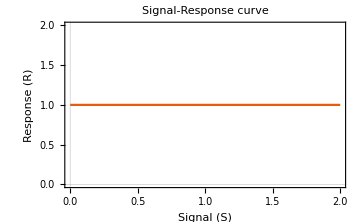

```mathematica
solPerfect = Solve[0 == (v1-v2) /. rateqsA,r];
perfectSignalResponse =Plot[r/.solPerfect⟦1⟧/.paramsA,
{s,0,2},
Frame->True,
FrameLabel->{"Signal (S)","Response (R)"},
PlotRange-> {{0,2}, {0,2}},PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"Scientific",
ImageSize->Medium]
```

As seen in the plot above, the signal response curve is just a straight line. This is because the function for the response is independent of S.

Next. we look at the three different types of feedback. First, negative feedback: homeostasis. The reaction rate is plotted, after which the signal response curve is generated.

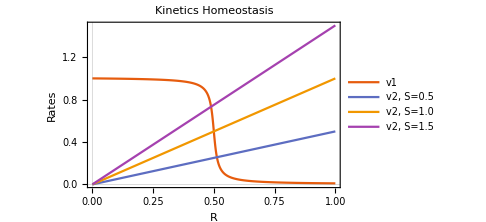

```mathematica
Remove[k0,k1,k2,k3,k4,J3,J4,s,r]

G[u_,v_,J_,K_]=2*u*K/(v-u+v*J+u*K+((v-u+v*J+u*K)^2-4*(v-u)*u*K)^0.5);

paramsHomeo={k0->1,k2->1,k3->0.5,k4->1,J3->0.01,J4->0.01};
equationsA={v1->k0*G[k3,k4*r,J3,J4], v2-> k2*s*r};

homeostasisKinetics = Plot[{v1/.equationsA/.paramsHomeo,
v2/.equationsA/.paramsHomeo/.s->0.5,v2/.equationsA/.paramsHomeo/.s->1,v2/.equationsA/.paramsHomeo/.s->1.5},
{r,0,1},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"R","Rates"}, 
PlotLabel-> Style["Kinetics Homeostasis", FontSize-> 18],
PlotLegends->{"v1","v2, S=0.5", "v2, S=1.0","v2, S=1.5"},
ImageSize->Medium]

solHomeo = Solve[0 == (v1-v2) /. equationsA,r];
homeostasisSignalResponse =Plot[r/.solHomeo⟦1⟧/.paramsHomeo,
{s,0,2},
Frame->True,
FrameLabel->{"Signal (S)","Response (R)"},
PlotRange-> {{0,2}, {0,1}},PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"Scientific",
ImageSize->Medium];
```

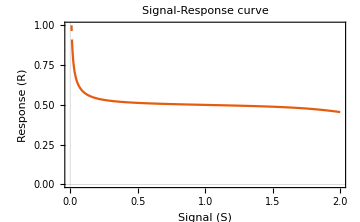

```mathematica
homeostasisSignalResponse
```

We see that v2 is the only rate that is dependent on S, and that is goes up as S goes up. Again, the equilibrium point stays at more or less the same place.

The response values are confined to a narrow window. This is because the homeostasis, or negative feedback loop, is self-regulating:the output of the system, R is fed back in a way that tends to reduce the fluctuations in the output: it counteracts the effect of the stimulus S. Another name for negative feedback is balancing feedback, which makes sense, because this type of feedback promotes stability.

Next, we plot the same graphs for Mutual Inhibition.

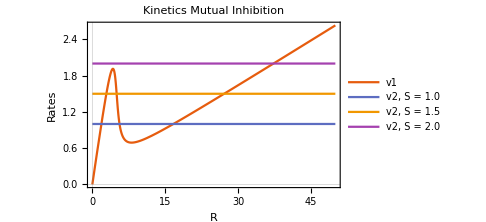

```mathematica
Remove[v1, v2, k0,k1,k2,k3,k4,J3,J4,s,r]

paramsInhibition={k0->0,k1->1,k2->0.05,k2b->0.5,k3->1,k4->0.2,J3->0.05,J4->0.05};
equationsB={v1-> k2*r+k2b*G[k3,k4*r,J3,J4]*r, v2->k0+k1*s};

mutualKinetics = Plot[{v1/.equationsB/.paramsInhibition, v2/.equationsB/.paramsInhibition/.s->1,v2/.equationsB/.paramsInhibition/.s->1.5,v2/.equationsB/.paramsInhibition/.s->2.0},{r,0,50},PlotTheme->"Scientific", 
PlotLabel-> Style["Kinetics Mutual Inhibition", FontSize-> 18],
Frame->True,
FrameLabel->{"R","Rates"}, 
PlotLegends->{"v1","v2, S = 1.0", "v2, S = 1.5","v2, S = 2.0"},
ImageSize-> Medium]

solInhibition = Solve[(v2 == v1) /. equationsB/.paramsInhibition,r];
signalResponseMutual = Plot[{r/.solInhibition⟦1⟧/.paramsInhibition, r/.solInhibition⟦2⟧/.paramsInhibition, r/.solInhibition⟦3⟧/.paramsInhibition},{s,0,2},
Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, PlotLabel->Style["Signal-Response curve", FontSize->18], PlotTheme->"Scientific",
PlotStyle->{{Orange, Dashed}, Orange, Orange} ,
PlotRange->{{0, 2},{0,30}},
Epilog->{Dashed, Gray, Line[{{{1.9, 0}, {1.9, 30}}, {{0.7,0},{0.7,30}}}]},
ImageSize->Medium];
```

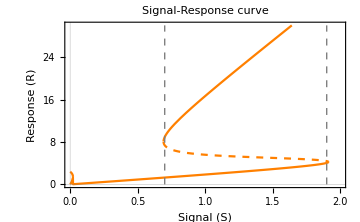

```mathematica
signalResponseMutual
```

We see that v2 is constant, but dependent on S, as it gets higher when S goes up. We see that the equilibrium points are dependent on S too; the locations differ, and also the amount of equilibrium points differ. For S = 2.0, there is only one equilibrium point, whereas for S=1.5 and 1.0 there are three. 

At the rates where v2 would intersect with the top/bottom of v1, there two equilibrium points: we call these the critical points. The feedback has created a toggle-switch. 

In the second graph, we see the Signal-Response curve, where the two vertical lines are the critical points. Part of the response curve is dashed: this is because this response strength can never exist. When S has decreased enough, the switch will go back to the off-state. Between the two critical values, the response of the system can be small or large.

Finally, we plot the same graphs for mutual activation.

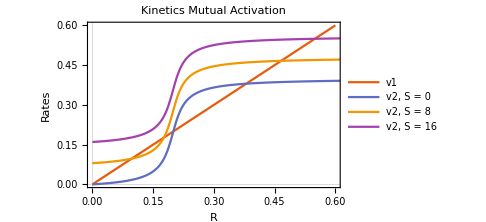

```mathematica
Remove[v1,v2,k0,k1,k2,k3,k4,J3,J4,s,r];

paramsActivation={k0->0.4,k1->0.01,k2->1,k3->1,k4->0.2,J3->0.05,J4->0.05};
equationsC={v2->k0*G[k3*r,k4,J3,J4]+k1*s,v1->k2*r};

kineticsActivation = Plot[{v1/.equationsC/.paramsActivation,v2/.equationsC/.paramsActivation/.s->0,v2/.equationsC/.paramsActivation/.s->8,v2/.equationsC/.paramsActivation/.s->16},{r,0,1},PlotRange->{{0,0.6},{0,0.6}},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"R","Rates"},
PlotLabel-> Style["Kinetics Mutual Activation", FontSize-> 18],
PlotLegends->{"v1","v2, S = 0", "v2, S = 8","v2, S = 16"},
ImageSize-> Medium]

solActivation=Solve[(v1== v2)/.equationsC/.paramsActivation,r];ResponseCurveActivation = Plot[{r/.solActivation⟦1⟧/.paramsActivation, r/.solActivation⟦2⟧/.paramsActivation, r/.solActivation⟦3⟧/.paramsActivation},{s,0,50},Frame->True,FrameLabel->{"Signal (S)","Response (R)"},PlotLabel->Style["Signal-Response curve",FontSize->18],PlotTheme->"Scientific", 
PlotRange->{{0, 15}, {0, 0.6}},
PlotStyle-> {{Orange, Dashed},Orange,Orange},
Epilog->{Dashed, Gray, Line[{{10.1, 0}, {10.1, 0.6}}]},
ImageSize->Medium];
```

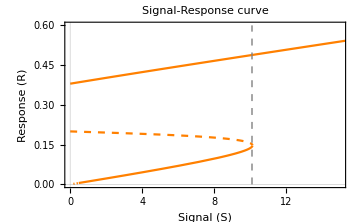

```mathematica
ResponseCurveActivation
```

Here we see that v2 is dependent on S. As S gets higher, the curve keeps having the same shape, but shifts upwards. We can also see that for different S, we have different (amounts of) equilibrium points.

In the signal-response curve, we see one critical point. The orange dashed line once again indicates the response strength can never exist. The feedback has created a discontinuous switch. This means that the cellular response changes abruptly as the signal magnitude crosses the critical value. This is irreversible. Between the values of S=0 and S_crit, the system is called bistable. 

Conclusions
In a feed-forward system, we see that the signal influences the response via two pathways. These push the response in opposite directions.

After studying these networks, we can conclude that figure 1b contains a model of positive feedback with mutual activation, figure 1c is positive feedback with mutual inhibition, and figure 1d is negative feedback or homeostasis. In figure 1d we see the negative feedback: the response R counteracts the effect of the stimulus S. In both 1b and 1c S enhances R, but in 1b R enhances also its own synthesis by phosphorylating E. This is called mutual activation. In 1c we see that R inhibits its own synthesis by phosphorylating E, and that is called mutual inhibition.

We see that with the (arbitrary) values for the parameters that we used , the negative feedback gets into a steady state concentration of the response R, and that it is confined to a narrow window for a broad range of signal strengths. We can also see that, in the case of mutual inhibition, the feedback creates a toggle switch. In the last case that we discussed, we see that a discontinuous switch is created. This is also called a one-way switch and plays major roles in developmental processes and cellular apoptosis, both characterized by a point-of-no-return.

## Case study: The Lac operon - A switch

An operon is a part of the DNA containing a cluster of genes controlled by a promotor. In this section of this study, we take a closer look at the Lac-operon of Escherichia Coli, which has a promotor that is repressed by a repressor in the absence of lactose. When lactose is available in the medium, lactose is imported and converted into allolactose. Allolactose is at his turn able to inhibite the inhibitor of the promotor, and thereby allows the RNA polymerase to bind the promotor; mRNA is subsequently produced. 

-Graphics-
Figure 2: Schematic of the lac operon. The top scheme (a) shows the active repressor binding the operator in the absence of (allo)lactose, therefore inhibiting the transcription of the lac genes. Bottom scheme (b) shows deactivation of the repressor by allolactose, thereby deblocking the operator opening the way for the transcription of the lac genes.    

It is assumed that the production of mRNA is proportional to its translation into the proteins (permease, β-galactosidase and transacetylase, see figure 2), and we can thus write the following system of ODEs as discussed in De Boer:

	ⅆM/ⅆt=k_1+k_2(1-1/(1 + A^n))-k_3 M
ⅆA/ⅆt=k_4 M L-k_5 A-V_max(M A)/(K_m + A)


Methods

In this section we take a closer look at the Lac operon. First, the different terms in the differential equations above are discussed. We touch upon both the positive and negative feedback loops. 

Next, the differential equations are solved with initial conditions M_0=0, A_0=0.05. The following parameter values are used: k_1=0.05, k_2=k_3=L=V_max=k_4=1, k_5=0.2,K_m=2,n=5. We take a look at the mRNA concentration and investigate what happens when increasing L from 1 to 3 with steps of 1. 

In order to analyse the  qualitative behavior and easily identify points for which the system resides in a steady-state, the isoclines are derived. These isoclines are curves for which the ODE equals 0. We attempt to find the isoclines for mRNA in terms of allolactose concentration. This is done for both equations. L is kept at a constant of 1. 

Finally, the equilibrium points for this system are determined and compared to those found in the earlier plot.

Stability Analysis
Biological systems can show different dynamic behaviours, ranging from stable to oscillating systems. If a system is at steady state, it should stay there, at least until an external perturbation occurs. Depending on the systems behavior after perturbation, their steady states can be: 
(a) stable (the system returns to this state),
(b) unstable (The system leaves this state) or 
(c) metastable (the system behavior is indifferent)

To investigate wheter a steady state of the ODE system is asymptotically stable, we need to linearize the system, and determine the eigenvalues of the Jacobian matrix. If the real parts of all eigenvalues are less than 0, i.e. negative (λ < 0), then the system is stable at that steady state. For two-dimensional systems, depending on the sign of the eigenvalues, the steady states (equilibrium points) can be distinguished: - Node: Both eigenvalues are real and of same sign.
	- Stable: values are negative
	-Unstable: values are positive
-Saddle: Both eigenvalues are real and of opposite sign. Saddle point is always unstable. 
-Focus (or Spiral point): When the eigenvalues are complex conjugates. 
	-Stable: values are negative real part
	-Unstable: values are positive real part  
-Center: Both eigenvalues are pure imaginary.  

Results and Discussion
When looking at the ODEs as defined in de Boer and in the introduction, we see that the first ODE shows that if A increases, the production of M increases. However, M has a negative effect on itself: if the production of M increases, the production of M decreases. 

The second ODE is a little bit more complicated. It becomes clear that A has a negative effect on itself, if the production of A increases, the production of A decreases. L has a positive influence on A as well, more is results in more A. M is a more complex story. The first part of the equation suggests that an increase of M increases the production of A. However, in the last part of the equation, M is involved in the breakdown of A.

Next, we solve the differential equations and see what happens when L increases.

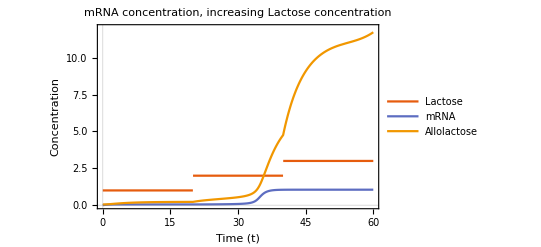

```mathematica
ClearAll["Global`*"]

k1 = 0.05;
k2 =  1;
k3 =  1;
L = 1;
Vmax =  1;
k4 =  1;
k5 = 0.2;
Km= 2;
n=5;

solved[t_] = NDSolve[{M'[t]== k1 + k2*(1- 1/(1+A[t]^n))-k3*M[t], A'[t]== k4*M[t]* (Floor[t/20]+1) - k5*A[t]-Vmax*M[t]*A[t]/(Km+A[t]), M[0]==0, A[0]==0.05}, {M[t],A[t]}, {t, 0 ,50}];

Plot[{Floor[t/20] + 1,M[t]/.solved[t], A[t]/.solved[t]}, {t,0,60}, PlotLegends-> {"Lactose", "mRNA", "Allolactose"}, 
PlotTheme->"Scientific",
Frame-> True,
FrameLabel->{"Time (t)", "Concentration"},
PlotLabel-> Style["mRNA concentration,\n increasing Lactose concentration", FontSize-> 18],
PlotRange->{{0,60},{0,12}}]
```

In the above plot, we see that when L = 1, the concentration of allolactose almost immediately increases (albeit by a small amount). The concentration of mRNA does not react immediately. This is expected, as lactose is needed to convert lactose to allolactose. Then, allolactose can go on to create more mRNA. Thus, an increase of L cannot immediately increase mRNA, as the lactose first needs to be converted into allolactose. The concentration of mRNA only increases after allolactose has been in the system for a certain amount of time. 

A further increase of L to 2 shows a drastic increase of the concentration of allolactose after a while. Once again, this is not surprising. Notice here how when allolactose has been in the system for a while the concentration of mRNA starts to increase. However, a drastic increase of allolactose does not equal a drastic increase of mRNA. 

When L is increased to 3, the increase in concentration  of allolactose seems to slowly level out. This might be because no more allolactose can be produced or no more is needed.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

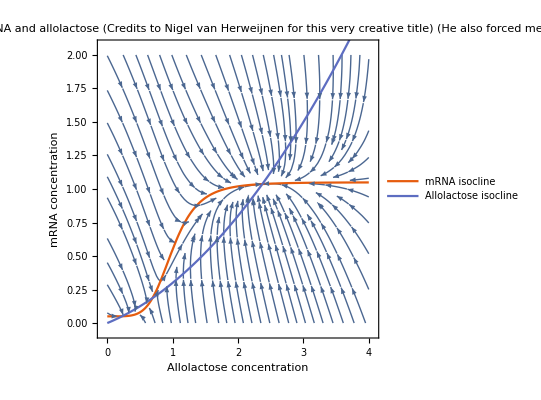

```mathematica
dM[A_, M_] = k1 + k2*(1- 1/(1+A^n))-k3*M;
dA[A_, M_] = k4*M* L - k5*A-Vmax*M*A/(Km+A);

streamplot = StreamPlot[{dA[A, M], dM[A, M]}, {A, 0, 4}, {M, 0, 2}, PlotLabel->"Isoclines in the streams of mRNA and allolactose \n (Credits to Nigel van Herweijnen for this very creative title) \n (He also forced me to give him credit)", FrameLabel-> {"Allolactose concentration", "mRNA concentration"}];

f1 = M/.Solve[dM[A, M] == 0];
f2 = M/.Solve[dA[A, M] == 0];
isoclines = Plot[{f1, f2}, {A, 0, 4}, 
PlotTheme->"Scientific",
PlotLegends-> {"mRNA isocline","Allolactose isocline"}];

Show[streamplot, isoclines]
```

In this plot, we see that the system has 3 equilibrium points: the intersections of the isoclines. Of these, only 2 are stable: one is not. We can see this because in middle equilibrium point, the direction of the arrows is away from the point: this means that a small perturbation will cause the system to leave this equilibrium. It is probably a saddle point, because of the shape of the graph: the arrows go down from two sides, and up on the other two sides. This should be confirmed by math: the eigenvalues should be real and of opposite sign.

Conclusions
We can conclude that the transcription of the mRNA starts when the Lactose concentration increases. This is because lactose is converted into allolactose, and this inhibits the inhibitor of the promotor, allowing RNA polymerase to bind to the promotor and thereby allowing RNA pollymerase to bind to the promotor and subsequently produce mRNA.

We can also see that there are three equilibrium points in this reaction, two of them are stable, and one is not. The starting concentrations determine in what equilibrium the reaction will end.

## Simple Boolean network Qualitative logical models

A Boolean network is a form of logical modeling. This form of modeling is based on the idea that variables can take on a finite set of values. In the case of a Boolean network 0 and 1. In most variants, time is not represented. State transitions take place at each time point, but a time step can represent different time durations for different transitions. 


Methods
In this section, a simple Boolean network and its behaviour is investigated. The Boolean network in question can be seen below.

The network contains three components (X, Y, Z) that all influence each other. Both X and Z are necessary to activate Y, Z deactivated X, Y activates Z and X also activates itself. 

First, the rules for this network are inferred after which the state transition table is generated. This is done by converting the rules of the network into functions of X, Y, and Z, and then iterating over all the possible values for X, Y, Z and converting the Boolean output into integers. 

After this, the state transition graph is generated. 

Results and Discussion
Looking at the above network, the following rules are inferred:

- X(t+1) = 1 	if 	NOT Z(t)
- X(t+1) = 0 	if 	Z(t)
- Y(t+1) = 1 	if 	X(t) 	AND Z(t)
- Y(t+1) = 0 	if 	NOT X(t) OR NOT Z(t)
- Z(t+1) = 1 	if 	Y(t)	
- Z(t+1) = 0 	if 	NOT Y(t)

Here, it is assumed that X is always activating itself, so the activation of X is only dependent on the activation of Z. Both X and Z are needed to activate Y, so if one of these is not activated at time step T, Y will not be activated in time step T + 1. 

From these rules, the state transition table is generated. Based on the graph above, this table  looks as follows:

```mathematica
ClearAll["Global`*"]
func1[x_,y_,z_]:=!z
func2[x_,y_,z_]:=x&&z
func3[x_,y_,z_]:=y

(*Generate a list of all possible states*)
statesList=Tuples[{{True,False},{True,False},{True,False}}];

(*Apply the rules to this states list*)
listTransition=Catenate[{Boole[statesList] // Transpose,{Boole[Apply[func1,statesList,1]],Boole[Apply[func2,statesList,1]],Boole[Apply[func3,statesList,1]]}}]//Transpose;

(*Make a nice readable table*)
TableForm[listTransition,TableHeadings->{Automatic,{"X(t)","Y(t)","Z(t)","X(t+1)","Y(t+1)","Z(t+1)"}},TableAlignments->Center]
```

| X(t) | Y(t) | Z(t) | X(t+1) | Y(t+1) | Z(t+1)
1 | 1 | 1 | 1 | 0 | 1 | 1
2 | 1 | 1 | 0 | 1 | 0 | 1
3 | 1 | 0 | 1 | 0 | 1 | 0
4 | 1 | 0 | 0 | 1 | 0 | 0
5 | 0 | 1 | 1 | 0 | 0 | 1
6 | 0 | 1 | 0 | 1 | 0 | 1
7 | 0 | 0 | 1 | 0 | 0 | 0
8 | 0 | 0 | 0 | 1 | 0 | 0

From this, the state transition graph looks as follows:

```mathematica
panelLabel[lbl_]:=Panel[lbl,FrameMargins->0.5,Background->Lighter[Pink,0.7]]

Graph[{1 -> 2,2-> 3,3-> 4, 4-> 5, 5-> 5},VertexLabels->{1-> Placed["111",Center,panelLabel],
2-> Placed["011",Center,panelLabel],
3-> Placed["001",Center,panelLabel],4-> Placed["000",Center,panelLabel],
5-> Placed["100",Center,panelLabel]},
EdgeStyle->Darker[Pink], PlotTheme->"Minimal"]

Graph[{ 1-> 2,2-> 1,3-> 2},VertexLabels->{1-> Placed["010",Center,panelLabel],
2-> Placed[" 101",Center,panelLabel],
3-> Placed["110",Center,panelLabel]},
EdgeStyle->Darker[Pink], DirectedEdges->True, PlotTheme->"Minimal"]
```

-Graphics-

-Graphics-

It is not possible to iterate through all the steps in the network from one starting point. Thus, two different graphs are necessary. 

In the first graph we start with all components are turned on (caused by whichever reason). This ensures that X is turned off in T + 1 (as Z is on in T). Then, because X is no longer on, Y will turn off in T + 2 (as it needs both X and Z). This causes Z to be turned off in T + 3, which causes X to turn on in T + 4. As X activates itself, and Y is needed to turn on Z to turn off X but Z is needed to turn on Y, the system is “stuck” in this state where X turned on. 

The second graph shows that the system keeps oscillating between state 010 and 101. This could be expected as both X and Z combined turn on Y in step T + 1. However, as Y is not on in step T, Z will turn off in T + 1. As Z is on in step T, X is turned off but will turn on once Z is off, as happens in T + 1. 

Conclusions
In this section, we took a closer look at a simple Boolean network. Generating the state transition table gave us insight into the behaviour of the network over time. Generating the state transition graph showed that the network can either get stuck in a situation where only X is active, or in a situation where the network oscillates between 101 and 010. Where the system ends up depends on where it started.